## Cavity detuning induced Quantum Sensor

```mathematica
Clear["Global`*"]
```

```mathematica
C0=1;
R0=3/5;
ham[δ_,R0_,G_]:={{δ+I G,R0,C0},{R0,0,R0},{C0,R0,δ-I G}};
ham[δ,R0,G]//MatrixForm
```

(ⅈ G+δ | 3/5 | 1
3/5 | 0 | 3/5
1 | 3/5 | -ⅈ G+δ)

```mathematica
compcond=Simplify[Discriminant[Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]]
```

-4 G^6+G^4 (516/25-8 δ^2)+(4 (16-25 δ)^2 (97+50 δ+25 δ^2))/15625+G^2 (-22188/625+(648 δ)/25+(8 δ^2)/5-4 δ^4)

```mathematica
Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,0];
```

-18/25+e^3+(18 δ)/25-2 e^2 δ+e (-43/25+G^2+δ^2)

```mathematica
realcond=(a1-3a0/a2)/2-(a2/3)^2;
```

```mathematica
engeq=With[{δ0=1/2},(Det[ham[δ,R0,G]-IdentityMatrix[3]e]/.Solve[Evaluate[realcond/.{δ->δ0}]==0,G∈Reals][[2]])/.{δ->δ0}]
Solve[engeq==0,e]//N
```

9/25-(293 e)/225+e^2-e^3

{{e→0.333333},{e→0.333333-0.984322 ⅈ},{e→0.333333+0.984322 ⅈ}}

```mathematica
Gc=(DeleteDuplicates[G/.Solve[{Numerator[Resultant[realcond,compcond,δ]]==0,G∈Reals,G>0},G]][[1]])
δc=(δ/.Solve[{Evaluate[realcond/.{G->Gc}]==0,δ∈Reals,δ>0},δ])[[1]]
e/.Solve[Det[ham[δc,R0,Gc]-e IdentityMatrix[3]]==0,e]//N
```

Root1.39Root[-410758+989625 #1^2-885000 #1^4+250000 #1^6&,2]1.3892973136473576

Root0.794Root[{-410758+989625 #1^2-885000 #1^4+250000 #1^6&,-243-144 #2+225 #1^2 #2+25 #2^3&},{2,1}]0.7940031971744785

{0.529335,0.529335,0.529335}

```mathematica
Solve[Simplify[Resultant[Simplify[D[compcond,δ]/D[compcond,G]],compcond,δ]]==0,G]
```

{{G→-1},{G→1}}

```mathematica
Gc1=G/.Solve[Evaluate[compcond/.{δ->0}]==0,G][[2,1]]
```

√(Root0.202Root[-24832+138675 #1-80625 #1^2+15625 #1^3&,1]0.20182120245685137)

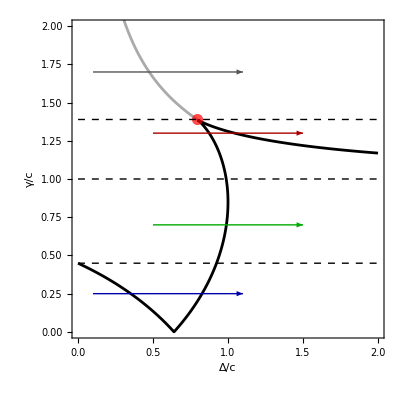

```mathematica
Show[ContourPlot[compcond==0,{δ,0,2},{G,0,2},PlotPoints->100,ContourStyle->Directive[Black,Thickness[0.005]]],ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Gray,(*Dashed,*)Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Opacity[0.7],Point[N@{δc,Gc}]}],
Graphics[{Dashed,Line[{{0,N@Gc},{2,N@Gc}}],Line[{{0,1},{2,1}}],Line[{{0,N@Gc1},{2,N@Gc1}}]}],
Graphics[{{Darker@Red,Arrowheads[0.04],Arrow[{{0.5,1.3},{1.5,1.3}}]},{Darker@Green,Arrowheads[0.04],Arrow[{{0.5,0.7},{1.5,0.7}}]},{Darker@Blue,Arrowheads[0.04],Arrow[{{0.1,0.25},{1.1,0.25}}]},{Darker@Gray,Arrowheads[0.04],Arrow[{{0.1,1.7},{1.1,1.7}}]}}],
Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"Δ/c","γ/c"}]
```

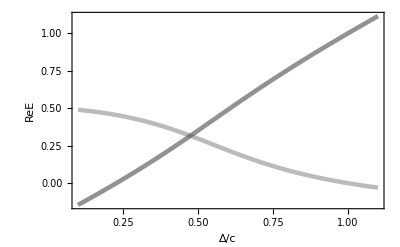

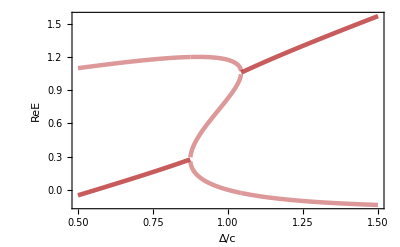

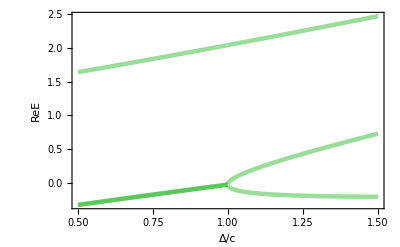

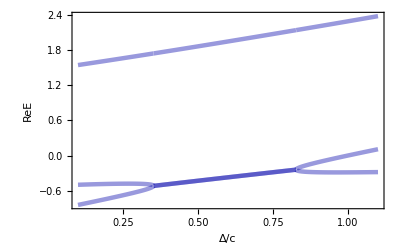

```mathematica
Plot[{Evaluate[Re[Eigenvalues[ham[δ,3/5,17/10]]]]},{δ,0.1,1.1},PlotStyle->{{Thickness[0.008],Darker@Gray,Opacity[0.4]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"Δ/c","ReE"}]
Plot[{Evaluate[Re[Eigenvalues[ham[δ,3/5,13/10]]]]},{δ,0.5,1.5},PlotStyle->{{Thickness[0.008],Darker@Red,Opacity[0.4]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"Δ/c","ReE"}]
Plot[{Evaluate[Re[Eigenvalues[ham[δ,3/5,8/10]]]]},{δ,0.5,1.5},PlotStyle->{{Thickness[0.008],Darker@Green,Opacity[0.4]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"Δ/c","ReE"}]
Plot[{Evaluate[Re[Eigenvalues[ham[δ,3/5,1/4]]]]},{δ,0.1,1.1},PlotStyle->{{Thickness[0.008],Darker@Blue,Opacity[0.4]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"Δ/c","ReE"}]
```